Jessica Yee
UID: 104938481
jessica23424@g.ucla.edu
HW4

```mathematica
(*Problem 1*)
Assuming[Element[n,Integers],DSolve[{x''[t]+2*beta*x'[t]+omega^2*x[t]==Sin[2Pi*n*t/(2Pi/omegap)]}, x[t],t]]
DSolve[{x''[t]+2*beta*x'[t]+omega^2*x[t]==Cos[2Pi*n*t/(2Pi/omegap)]}, x[t],t]
```

{{x[t]→ⅇ^((-beta-√(beta^2-omega^2)) t) C[1]+ⅇ^((-beta+√(beta^2-omega^2)) t) C[2]+(2 beta n omegap Cos[n omegap t]-omega^2 Sin[n omegap t]+n^2 omegap^2 Sin[n omegap t])/((-2 beta^2+omega^2+2 beta √(beta^2-omega^2)-n^2 omegap^2) (2 beta^2-omega^2+2 beta √(beta^2-omega^2)+n^2 omegap^2))}}

{{x[t]→ⅇ^((-beta-√(beta^2-omega^2)) t) C[1]+ⅇ^((-beta+√(beta^2-omega^2)) t) C[2]+(-omega^2 Cos[n omegap t]+n^2 omegap^2 Cos[n omegap t]-2 beta n omegap Sin[n omegap t])/((-2 beta^2+omega^2+2 beta √(beta^2-omega^2)-n^2 omegap^2) (2 beta^2-omega^2+2 beta √(beta^2-omega^2)+n^2 omegap^2))}}

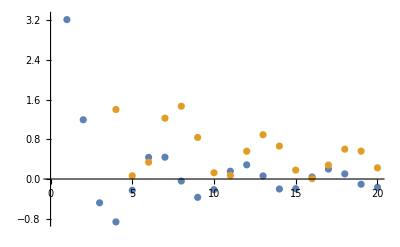

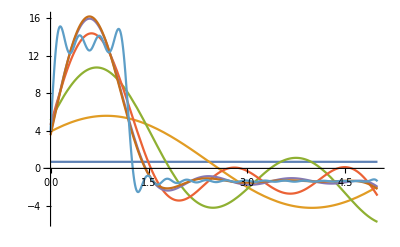

```mathematica
(*Problem 2*)
Remove["Global`*"]
 Assuming[Element[n,Integers],An[n_]:=2/T*F0*Sin[n*c*T]/n/T]
 Assuming[Element[n,Integers],Bn[n_]:=2*F0/n/T*(1-Cos[n*c*T])]
Assuming[0<c<1,F[t_,i_]:=(T*c)/T+ Sum[An[n]*Cos[n*t]+Bn[n]*Sin[n*t],{n,1,i}]]
F0=5.0;  c=0.7;
T=1.7;
x={}; a={}; b={};
For[i=1,i<21,i++,x= Append[x,i]; a=Append[a,An[i]]; b=Append[b, Bn[i]]] ;
ListPlot[{a,b}]
Plot[{F[t,0],F[t,1],F[t,2], F[t,3],F[t,4],F[t,5],F[t,20]},{t,0,5}]
```

```mathematica
(*Problem 3*)
Clear[x]
omegan=2*Pi;
beta=0.05*omegan;
f[t_]:=F[t,20];
DSolve[{x''[t]+2*beta*x'[t]+omegan^2*x[t]==f[t], x[0]==0, x'[0]==0},x[t],t]
```

{{x[t]→(0.00197624+0.0185465 ⅈ) ⅇ^((-0.628319-6.27533 ⅈ) t) ((0.21072-0.977547 ⅈ) ⅇ^(0.314159 t)-(0.+1. ⅈ) ⅇ^((0.314159+12.5507 ⅈ) t)+(3.17057+0.964109 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t]+(3.91726-0.352394 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[1. t] Cos[3. t]+(2.82882-1.90638 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[2. t] Cos[3. t]+(0.100729-0.945309 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t]^2-(0.242569-2.27644 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[4. t]-(2.36359+2.45966 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t] Cos[4. t]-(0.0900742-0.845321 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[5. t]-(3.75505+1.16993 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t] Cos[5. t]+(0.0519004-0.487071 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[6. t]-(3.30254-0.274359 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t] Cos[6. t]-(0.494371-4.63953 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[7. t]-(0.057725-0.541733 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[8. t]+(0.0342271-0.321212 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[9. t]+(0.0186493-0.175019 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[10. t]-(0.0113029-0.106075 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[11. t]-(0.0176164-0.165325 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[12. t]-(0.00519914-0.0487924 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[13. t]+(0.00593444-0.055693 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[14. t]+(0.0056474-0.0529993 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[15. t]-(0.00107984-0.010134 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[16. t]-(0.00481494-0.0451868 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[17. t]-(0.00254847-0.0239167 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[18. t]+(0.00149601-0.0140396 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[19. t]+(0.00252279-0.0236757 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[20. t]+(0.352394+3.91726 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t] Sin[1. t]+(1.90638+2.82882 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t] Sin[2. t]+(0.964109-3.17057 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[3. t]-(0.352394+3.91726 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[1. t] Sin[3. t]-(1.90638+2.82882 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[2. t] Sin[3. t]-(2.45966-2.36359 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[4. t] Sin[3. t]-(1.16993-3.75505 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[5. t] Sin[3. t]+(0.274359+3.30254 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[6. t] Sin[3. t]+(3.91726-0.352394 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[1. t] Sin[3. t]+(2.82882-1.90638 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[2. t] Sin[3. t]+(0.100729-0.945309 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[3. t]^2+(0.312924-2.93671 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[4. t]+(2.45966-2.36359 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t] Sin[4. t]-(2.36359+2.45966 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[3. t] Sin[4. t]+(0.0058413-0.054819 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[5. t]+(1.16993-3.75505 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t] Sin[5. t]-(3.75505+1.16993 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[3. t] Sin[5. t]+(0.60889-5.71426 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[6. t]-(0.274359+3.30254 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Cos[3. t] Sin[6. t]-(3.30254-0.274359 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[3. t] Sin[6. t]-(0.502758-4.71825 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[7. t]-(0.328083-3.07897 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[8. t]-(0.119276-1.11937 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[9. t]-(0.0137482-0.129023 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[10. t]-(0.00403484-0.0378659 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[11. t]-(0.0291644-0.2737 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[12. t]-(0.0388055-0.364179 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[13. t]-(0.0244285-0.229255 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[14. t]-(0.00580257-0.0544555 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[15. t]-(0.000124259-0.00116613 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[16. t]-(0.00618121-0.058009 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[17. t]-(0.011913-0.1118 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[18. t]-(0.00998143-0.093673 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[19. t]-(0.00362957-0.0340625 ⅈ) ⅇ^((0.628319+6.27533 ⅈ) t) Sin[20. t])}}

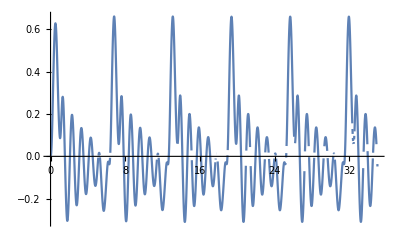

```mathematica
Plot[(0.001976240615231422+0.01854646778978296 ⅈ) ⅇ^((-0.6283185307179586-6.275326410661564 ⅈ) t) ((0.21071978601828228-0.9775465061982561 ⅈ) ⅇ^(0.3141592653589791 t)-(0.+1. ⅈ) ⅇ^((0.3141592653589795+12.550652821323128 ⅈ) t)+(3.1705728244413054+0.9641093637891144 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t]+(3.9172645899363023-0.35239350679113546 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[1. t] Cos[3. t]+(2.8288166354979807-1.9063802624432507 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[2. t] Cos[3. t]+(0.1007285111157107-0.9453090238718517 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t]^2-(0.24256891354849688-2.276441698068744 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[4. t]-(2.3635877777350327+2.459663001153791 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t] Cos[4. t]-(0.09007416869852497-0.8453209875271404 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[5. t]-(3.7550520294011043+1.169926197538987 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t] Cos[5. t]+(0.051900377111585655-0.4870705849069501 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[6. t]-(3.302539306015589-0.2743593130434239 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t] Cos[6. t]-(0.49437085912620826-4.639532830326887 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[7. t]-(0.057725020399976734-0.5417332400019264 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[8. t]+(0.03422708664743792-0.3212116759226123 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[9. t]+(0.01864933013240505-0.17501876944330286 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[10. t]-(0.011302923540284573-0.10607478955477256 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[11. t]-(0.017616392427844893-0.1653249367597596 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[12. t]-(0.005199135245381424-0.048792436315705706 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[13. t]+(0.0059344376386174826-0.055693044494081585 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[14. t]+(0.005647400772031343-0.05299928344110543 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[15. t]-(0.0010798432010117555-0.010134027704534056 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[16. t]-(0.004814935416328024-0.04518682791991685 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[17. t]-(0.002548470958673655-0.02391669019650391 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[18. t]+(0.0014960085180141147-0.014039623302317911 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[19. t]+(0.0025227878847825444-0.023675661700786964 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[20. t]+(0.35239350679113546+3.9172645899363023 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t] Sin[1. t]+(1.9063802624432507+2.8288166354979807 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t] Sin[2. t]+(0.9641093637891144-3.1705728244413054 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[3. t]-(0.35239350679113546+3.9172645899363023 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[1. t] Sin[3. t]-(1.9063802624432507+2.8288166354979807 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[2. t] Sin[3. t]-(2.459663001153791-2.3635877777350327 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[4. t] Sin[3. t]-(1.169926197538987-3.7550520294011043 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[5. t] Sin[3. t]+(0.2743593130434239+3.302539306015589 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[6. t] Sin[3. t]+(3.9172645899363023-0.35239350679113546 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[1. t] Sin[3. t]+(2.8288166354979807-1.9063802624432507 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[2. t] Sin[3. t]+(0.1007285111157107-0.9453090238718517 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[3. t]^2+(0.3129240769181097-2.9367053123385345 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[4. t]+(2.459663001153791-2.3635877777350327 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t] Sin[4. t]-(2.3635877777350327+2.459663001153791 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[3. t] Sin[4. t]+(0.005841304636207451-0.05481901720405939 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[5. t]+(1.169926197538987-3.7550520294011043 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t] Sin[5. t]-(3.7550520294011043+1.169926197538987 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[3. t] Sin[5. t]+(0.6088898549161105-5.714261712207965 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[6. t]-(0.2743593130434239+3.302539306015589 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Cos[3. t] Sin[6. t]-(3.302539306015589-0.2743593130434239 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[3. t] Sin[6. t]-(0.5027583212320537-4.718246826277149 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[7. t]-(0.32808346302588093-3.0789719290621 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[8. t]-(0.11927552439899647-1.1193675781814714 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[9. t]-(0.013748192314432351-0.1290229559913697 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[10. t]-(0.00403484334833616-0.03786588111790926 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[11. t]-(0.029164428360910856-0.27370003785684044 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[12. t]-(0.03880546822152056-0.36417851191343964 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[13. t]-(0.02442851339072141-0.22925479481669356 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[14. t]-(0.005802571852896645-0.05445552081978977 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[15. t]-(0.00012425865531556259-0.0011661328740285772 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[16. t]-(0.006181213843206408-0.058008970446831745 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[17. t]-(0.011912969986634695-0.11179990555547746 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[18. t]-(0.009981432269545301-0.09367296201497409 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[19. t]-(0.003629567535703006-0.034062480485896995 ⅈ) ⅇ^((0.6283185307179586+6.275326410661564 ⅈ) t) Sin[20. t]),{t,0,35}]
```

```mathematica
(*Problem 4*)
X[t_]:=Simplify[Assuming[{F0>0, Element[m, Reals], m>0},F0/m/omega1*Integrate[Exp[-gamma*u]Sin[omega*u]*Exp[-beta*(t-u)]Sin[omega1*(t-u)],u]]]
```

```mathematica
Simplify[X[t]-X[0]]
```

1/(2 m omega1)F0 (ⅇ^((beta-gamma) u) (((beta-gamma) Cos[(omega-omega1) u]+(omega-omega1) Sin[(omega-omega1) u])/(beta^2-2 beta gamma+gamma^2+(omega-omega1)^2)-((beta-gamma) Cos[(omega+omega1) u]+(omega+omega1) Sin[(omega+omega1) u])/(beta^2-2 beta gamma+gamma^2+(omega+omega1)^2))+ⅇ^(-beta t+beta u-gamma u) (((-beta+gamma) Cos[omega1 (t-u)+omega u]+(-omega+omega1) Sin[omega1 (t-u)+omega u])/(beta^2-2 beta gamma+gamma^2+(omega-omega1)^2)+((beta-gamma) Cos[omega1 t-(omega+omega1) u]-(omega+omega1) Sin[omega1 t-(omega+omega1) u])/(beta^2-2 beta gamma+gamma^2+(omega+omega1)^2)))